-(ⅈ (-1-ⅈ Cs R ω+Cs L ω^2))/(ω (-Cp-Cs-ⅈ Cp Cs R ω+Cp Cs L ω^2))

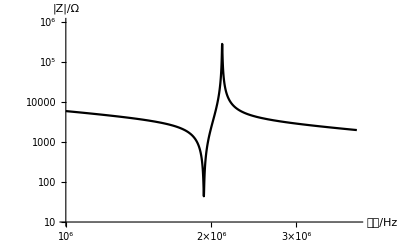

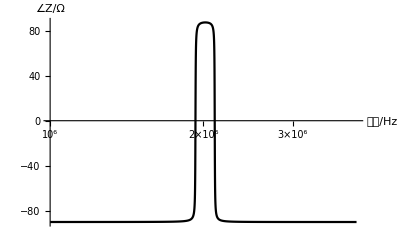

```mathematica
ClearAll[Cp,Cs,L,R];
Par[x_,y_]:=(x y)/(x+y);
Z[ω_]:=Par[1/(ⅈ ω Cp),ⅈ ω L+1/(ⅈ ω Cs)+R];
(*Z[ω_]:=Par[Rs+ⅈ ω L,1/(ⅈ ω Cp)];*)
Factor[Simplify[Z[ω],Element[{Cp,Cs,L,R,ω},Reals]]]
L=0.0017;R=44;Cp=21*10^-12;Cs=4*10^-12;(*murata ceralock 2.0MHz*)
LogLogPlot[Abs[Z[2 π f]],{f,10^6,4*10^6},PlotRange->{10,10^6},PlotTheme->"Monochrome",AxesLabel->{"频率/Hz","|Z|/Ω"}]
LogLinearPlot[Arg[Z[2 π f]]*180/π,{f,10^6,4*10^6},PlotRange->All,PlotTheme->"Monochrome",AxesLabel->{"频率/Hz","∠Z/Ω"}]
```

```mathematica
R=44;
FindMinimum[Abs[Z[2*π*f]],{f,2000000}]
```

FindMinimum::lstol: The line search decreased the step size to within the tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

{43.9945,{f→1.93001×10^6}}